# Mathematica Assignment 1

## ACM 40730: Mathematica for research

## Azam Jainullabudin Mohamed (18201501)

Assignment Handed in date : 13th September 2018
Assignment Due date              :  20th September 2018

## Basics

### 1. Entering and figuring out the below expressions.

```mathematica
Exp[ⅈπ]
```

ⅇ^ⅈπ

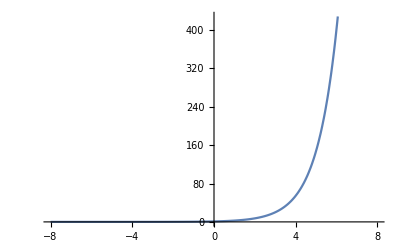

```mathematica
Plot[ⅇ^ⅈπ,{ⅈπ,-8,8}]
```

Enter the command “Exp” for importing exponential function base e.

Use the keyboard shortcut Esc-ii-Esc for importing Imaginary I.

Import shortcut Esc-p-Esc for using Pi.

```mathematica
8^(1/3)
```

2

Shortcut for square root is ctrl-2 .

Shortcut for entering the power value is ctrl-5.

Integrate::nodiffd: ∫_0^(2  π)  cannot be interpreted. Integrals are entered in the form ∫f ⅆx, ∫_a^b , or ∫_(vars ∈ region) , where ⅆ is entered as EscddEsc.

```mathematica
∫_0^(2π) Cos[θ]ⅆθ
```

```mathematica
0
```

For integral, use Esc-dintt-Esc.

Enter the limits with Esc-p-Esc for the pi in upper limit.

Enter the cosine function using keyword Cos.

Theta using keyword Esc-th-Esc.

### 2. Equivalent expression form from the text expressions

```mathematica
InputForm[HoldForm[π]]
```

HoldForm[Pi]

```mathematica
InputForm[HoldForm[Pi]]
```

HoldForm[Pi]

```mathematica
InputForm[HoldForm[Expr[Pi]]]
```

HoldForm[Expr[Pi]]

```mathematica
InputForm[HoldForm[ⅇ^π]]
```

HoldForm[E^Pi]

```mathematica
cos(Pi)sin(Pi)
```

cos π^2 sin

```mathematica
cos(π) sin(π)
```

cos π^2 sin

```mathematica
InputForm[Sqrt[2]]
```

Sqrt[2]

```mathematica
InputForm[√2]
```

Sqrt[2]

```mathematica
Sqrt[2] * Pi * r
```

√2 π r

```mathematica
√2 πr
```

√2 πr

### 3. Determining the meaning of N,I, E, C and D.

N - used for Numerical evaluation of expression.
       Keyboard shortcut is N.

```mathematica
N[10/4]
```

2.5

I - Represents the Imaginary unit Sqrt[-1]
     Keyboard shortcut for I is Esc-ii-Esc.

```mathematica
ⅈ
```

ⅈ

E - Represents the exponential constant with numerical value of 2.71828.
       Keyboard shortcut is Esc-ee-Esc

```mathematica
N[ⅇ, 10]
```

2.718281828

C - Constant generated in expressing various symbolic computations.
Its set by default for options GeneratedParameters in functions DSolve, RSolve, Reduce.

```mathematica
Reduce[Sin[x] == 1, x]
```

C[1]∈ℤ&&x==π/2+2 π C[1]

D - Represents derivative for univariate functions
       keyboard shortcut is Esc-pd-Esc

```mathematica
D[x^5, x]
```

5 x^4

### 4. Identifying the operations for addition, subtraction, multiplication, division, power, root, factorial and negotiation

Addition

Operator used for addition is ‘+’ operator.

```mathematica
150 + 38
```

188

Subtraction

Operator used for subtraction is ‘-‘ operator

```mathematica
100 - 45
```

55

Multiplication

Operator used for Multiplication is ‘*’ operator

```mathematica
23 * 5
```

115

Division

Operator used for division is ‘%’ operator

```mathematica
625%25
```

21484375

Power

Operator used for division is ‘^’ operator.

```mathematica
5 ^ 5
```

3125

Root

Operator used for division is ‘Square root’ operator

```mathematica
√625
```

25

Factorial

Operator used for division is ‘!’ operator

```mathematica
10!
```

3628800

Negotiation

Operator used for Negotiation is ‘Not’ operator

```mathematica
Not[8]
```

!8

### 5. Listing the functions involved in the above operations.

Add -> Function used for addition is ‘Plus’ function.

```mathematica
Plus[190,75]
```

265

Subtraction -> Function used for subtraction is ‘Subtract’

```mathematica
Subtract[100, 67]
```

33

Multiplication -> Function used for multiplication is ‘Times’ (shortcut - Esc-*-Esc)

```mathematica
Times[5, 125]
```

625

Division -> Function used for division is ‘Divide’ (shortcut - Esc-div-Esc)

```mathematica
Divide[100, 5]
```

20

Power -> Function used for identifying the  power value is ‘Power’

```mathematica
Power[5, 5]
```

3125

Root - > Function used for square root  is ‘Sqrt’

```mathematica
Sqrt[625]
```

25

Factorial -> Function used for factorial is ‘Factorial’

```mathematica
Factorial[5]
```

120

Negotiation -> Function used for Negotiation is ‘

```mathematica
!8
```

!8

## Expressions using Precedence rules

```mathematica
10/3*3
```

10

From the precedence rule, it evident that the division operator holds higher precedence than multiplication. 
Hence, validation will be (10/3)*3 as a result of it the output is 10.

```mathematica
-3^2
```

-9

According to precedence rule, precedence of Power > Subtraction. Hence, 3^2 is first performed and
- is multiplied to the output.

```mathematica
-1!
```

```mathematica
-1
```

Same as above, since Factorial weighs high precedence that subtraction, and so the express is rewritten as -(1!).

```mathematica
-2.5^(1/4)
```

-1.25743

As per precedence rule, since power’s  precedence is higher than Minus. Validation is performed as below
-(2.5^(1/4)) and hence the output holds a -ve symbol with its value.

```mathematica
(-2.5)^(1/4)
```

0.88914+0.88914 ⅈ

In the above case, because of parenthesis (-2.5), ‘-‘ is not treated as separate operator, hence the value
results in complex form with imaginary term.

```mathematica
1 +2*3-4/5+6
```

61/5

From the operator precedence, the evaluation is rewritten as 1+(2*3)-(4/5)+6 as per precedence.
Hence, the parenthesis is first solved first followed by next.

```mathematica
(1+2*3-4)/5+6
```

33/5

As above, parenthesis is first solved as below.
(1+(2*3)-4) = 3 and (3/5)+6 helps in getting the expected output.